## Prime Numbers

Part A)

```mathematica
primeCount=0
For[i=1, i<=100, i++,
If[PrimeOmega[i]==1, primeCount++]
]
Print["There are ",primeCount, " prime numbers."]
```

0

There are 25 prime numbers.

Part B)

```mathematica
F1[x_]:=2^x-1
primeCount2=0
For[i=1, i<=20, i++,
If[PrimeOmega[F1[i]]==1,primeCount2++]
]
Print["There are ",primeCount2, " prime numbers."]
```

0

There are 7 prime numbers.

## Gaussian Distribution

Part A)

```mathematica
(*Let x bar be represented as y, and delta x as z*)

F2[x_]=c*E^((-(x-y)^2)/(2z^2))
```

c ⅇ^(-(x-y)^2/(2 z^2))

```mathematica
Subs = {c-> 1, y->0, z->1}
F2[x]/.Subs
```

{c→1,y→0,z→1}

ⅇ^(-x^2/2)

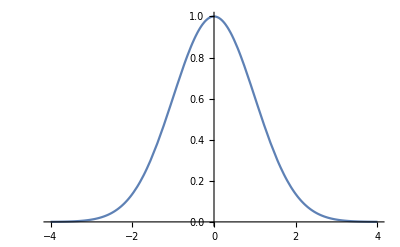

```mathematica
Plot0 = Plot[F2[x]/.Subs,{x,-4,4}]
```

Part B)

{c→1,y→1,z→1}

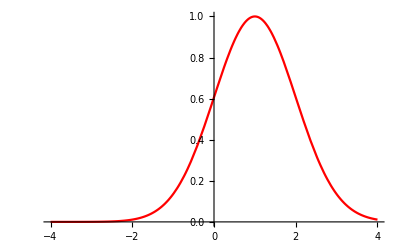

```mathematica
Subs1 = {c-> 1, y->1, z->1}
Plot1 =Plot[F2[x]/.Subs1,{x,-4,4},PlotStyle->Red]
```

{c→1,y→2,z→1}

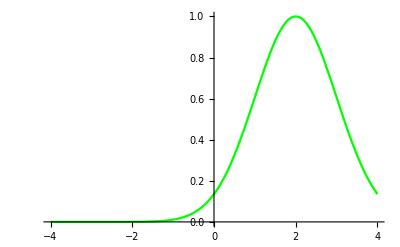

```mathematica
Subs2 = {c-> 1, y->2, z->1}
Plot2=Plot[F2[x]/.Subs2,{x,-4,4},PlotStyle->Green]
```

{c→1,y→1,z→2}

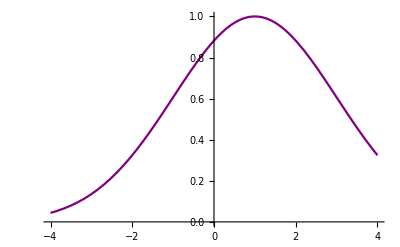

```mathematica
Subs3 = {c-> 1, y->1, z->2}
Plot3=Plot[F2[x]/.Subs3,{x,-4,4},PlotStyle->Purple]
```

{c→1,y→1,z→3}

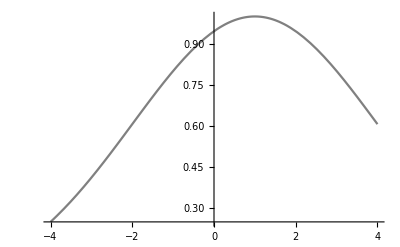

```mathematica
Subs4 = {c-> 1, y->1, z->3}
Plot4=Plot[F2[x]/.Subs4,{x,-4,4},PlotStyle->Gray]
```

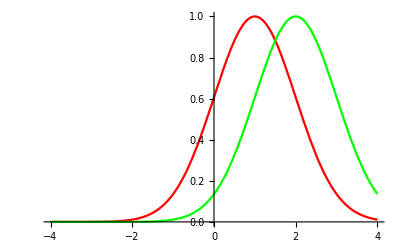

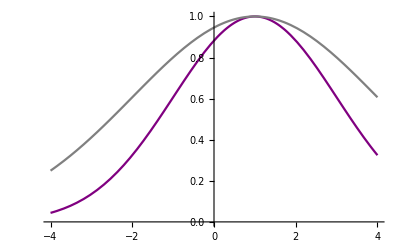

```mathematica
Show[Plot1,Plot2]
Show[Plot3,Plot4]
```

```mathematica
(*As xbar (or y) increases, the distribution shifts to the right.
As deltax (or z) increases the distribution flattens.*)
```

Part C)

```mathematica
F2[x]
Integrate[F2[x],{x, -∞, ∞},Assumptions->z>0]
(*The Assumptions parameter makes it so that the output is no longer conditional*)
```

c ⅇ^(-(x-y)^2/(2 z^2))

c √(2 π) z

```mathematica
solutionForC = Solve[c √(2 π)z==1,c]
```

{{c→1/(√(2 π) z)}}

Part D)

```mathematica
Subs5 = {c -> 1/(√(2 π)z)} (*Substituting our solution for c into original function*)
F2[x]/.Subs5
```

{c→1/(√(2 π) z)}

(ⅇ^(-(x-y)^2/(2 z^2)))/(√(2 π) z)

```mathematica
Print["The fraction of the distribution that is within +/-2.5z of the mean is ",Integrate[F2[x]/.Subs5,{x, y-2.5z, y+2.5z}]]
```

The fraction of the distribution that is within +/-2.5z of the mean is 0.987581

## Dice

Part A)

{}

{}

0

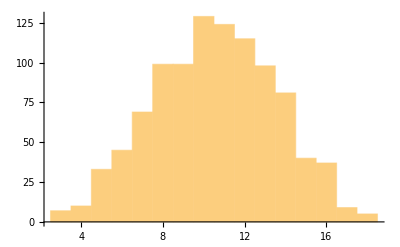

5

```mathematica
RollList={}
SumData={}
NumberOf18=0
For[i=1, i<=1000,i++,DiceRoll={RandomInteger[{1,6}],RandomInteger[{1,6}],RandomInteger[{1,6}]};
SumofDice = Part[DiceRoll,1]+Part[DiceRoll,2]+Part[DiceRoll,3];
(*Instead of using Part[] to index, could do Total[SumofDice]*)
RollList=Append[RollList,DiceRoll];
SumData=Append[SumData,SumofDice];
If[SumofDice==18,NumberOf18++]
]
Histogram[SumData]
NumberOf18
```

Part B)

```mathematica
$RecursionLimit=1000000;
TotalNumberOf18=0
NumberOfGames=0
For[k=1,k<=1000,k++,
NumberOf18=0;
For[i=1, i<=1000,i++,DiceRoll={RandomInteger[{1,6}],RandomInteger[{1,6}],RandomInteger[{1,6}]};
SumofDice = Part[DiceRoll,1]+Part[DiceRoll,2]+Part[DiceRoll,3];
If[SumofDice==18,NumberOf18++]
];
NumberOfGames++;
TotalNumberOf18=TotalNumberOf18+NumberOf18;
]
TotalNumberOf18
NumberOfGames
AverageNumberOf18=TotalNumberOf18/NumberOfGames
```

0

0

4699

1000

4699/1000

```mathematica
Print["On average, we can expect to roll a triple-6 approximately ", N[AverageNumberOf18], " times in a game."]
```

On average, we can expect to roll a triple-6 approximately 4.699 times in a game.

Part C)

```mathematica
TheoreticalNumberOf18 = 1000*((1/6)^3)
```

125/27

```mathematica
PercentError=100*Abs[(AverageNumberOf18-TheoreticalNumberOf18)/TheoreticalNumberOf18]
```

1873/1250

```mathematica
Print["The percent error in our experimental average for the number of triple-6 rolls is ",N[PercentError],"%."," This shows that our experimental average matches the theoretical value very closely."]
```

The percent error in our experimental average for the number of triple-6 rolls is 1.4984%. This shows that our experimental average matches the theoretical value very closely.